```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\yurra\Documents\memristive-brain\experiments\memristor measurement

```mathematica
Import[StringTemplate["1.csv"]]
```

Import::chtype: First argument TemplateObject[{1.csv},InsertionFunction→TextString,CombinerFunction→StringJoin] is not a valid file, directory, or URL specification.

$Failed

```mathematica
Clear[pulse]
```

```mathematica
pulse={}
```

{}

```mathematica
For[i=1,
i<16,i++, 
file=Import[StringTemplate["`a`.csv"][<|"a"->i|>]];
file[[All,1]]=file[[All,1]]+Abs[file[[1,1]]]*(2*i-1);
pulse=Join[pulse,file[[All,{1,2}]]]
 ]
```

```mathematica
Dimensions[pulse]
```

{37245,2}

```mathematica
Clear[resistance]
```

```mathematica
resistance={}
```

{}

```mathematica
For[i=1,
i<16,i++, 
file=Import[StringTemplate["C:\\Users\\yurra\\Documents\\Wolfram Mathematica\\meas\\`a`.csv"][<|"a"->i|>]];
file[[All,1]]=file[[All,1]]+Abs[file[[1,1]]]*(2*i-1);
resistance=Join[resistance,file[[All,{1,4}]]]
 ]
```

```mathematica
Dimensions[resistance]
```

{37245,2}

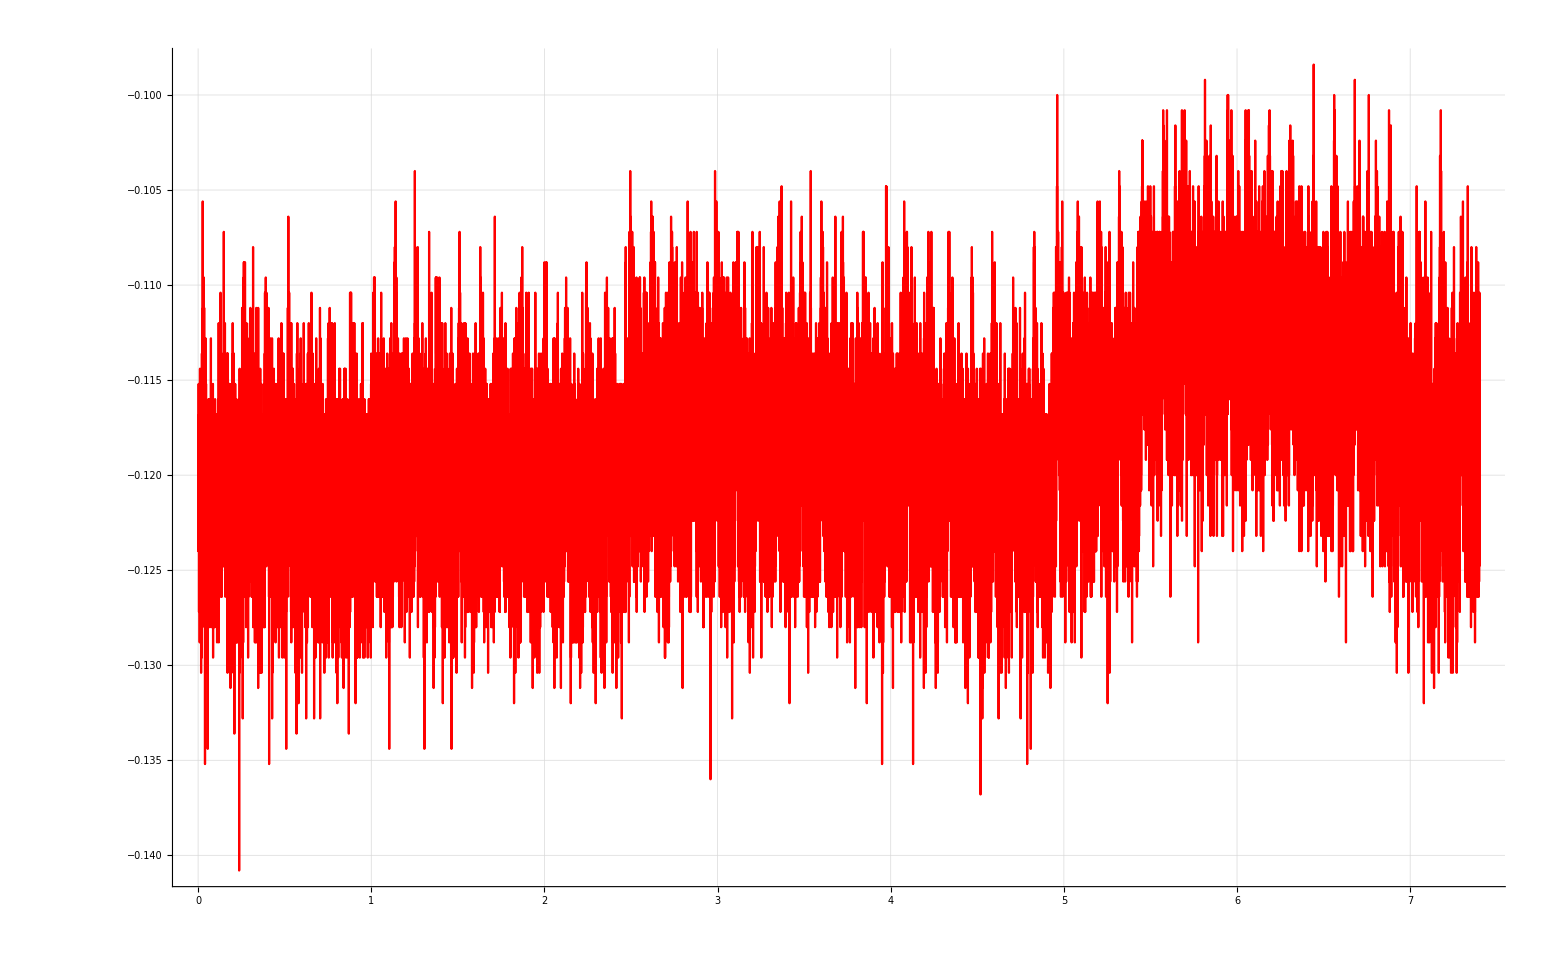

```mathematica
ListLinePlot[resistance,PlotStyle->Red,AxesStyle->Directive[Blue,12],GridLines->Automatic]
```